# Computing ω^(2)

In this file, we analytically compute the coefficient ω^(2)=1/2 from our paper. Recall the coefficients ω^(d) appear in the expansion of the variance of the Renyi-2 entropy in the equal squeezing regime. We prove that ω^(2)=1/2 by using the unitary Haar integrator Mathematica package RTNI by Fukuda, Koenig, and Nechita. The source is on GitHub, https://github.com/MotohisaFukuda/RTNI, and their paper is on arXiv, https://arxiv.org/abs/1902.08539. In order to run this file, you ill need to download the RTNI package.

### Clear all variables

```mathematica
Remove["RTNI`*"];
Remove["Global`*"];
```

Remove::rmptc: Symbol cloneGraph is Protected and cannot be removed.

Remove::rmptc: Symbol converttomonomial is Protected and cannot be removed.

Remove::rmptc: Symbol doi is Protected and cannot be removed.

General::stop: Further output of Remove::rmptc will be suppressed during this calculation.

### Import RTNI package

```mathematica
SetDirectory[NotebookDirectory[]];
<<RTNI`
```

Package RTNI (Random Tensor Network Integrator) version 1.0.5 (last modification: 26/01/2019).

Loading precomputed Weingarten Functions from /precomputedWG/functions1.txt

Loading precomputed Weingarten Functions from /precomputedWG/functions2.txt

Loading precomputed Weingarten Functions from /precomputedWG/functions3.txt

Loading precomputed Weingarten Functions from /precomputedWG/functions4.txt

Loading precomputed Weingarten Functions from /precomputedWG/functions5.txt

Loading precomputed Weingarten Functions from /precomputedWG/functions6.txt

Loading precomputed Weingarten Functions from /precomputedWG/functions7.txt

Loading precomputed Weingarten Functions from /precomputedWG/functions8.txt

Loading precomputed Weingarten Functions from /precomputedWG/functions9.txt

Loading precomputed Weingarten Functions from /precomputedWG/functions10.txt

Loading precomputed Weingarten Functions from /precomputedWG/functions11.txt

Loading precomputed Weingarten Functions from /precomputedWG/functions12.txt

Loading precomputed Weingarten Functions from /precomputedWG/functions13.txt

Loading precomputed Weingarten Functions from /precomputedWG/functions14.txt

Loading precomputed Weingarten Functions from /precomputedWG/functions15.txt

Loading precomputed Weingarten Functions from /precomputedWG/functions16.txt

Loading precomputed Weingarten Functions from /precomputedWG/functions17.txt

Loading precomputed Weingarten Functions from /precomputedWG/functions18.txt

Loading precomputed Weingarten Functions from /precomputedWG/functions19.txt

Loading precomputed Weingarten Functions from /precomputedWG/functions20.txt

## Comp function

Since Π is a projector, Π^2=Π. Similarly, Πᵀ=Π. This dramatically simplifies the result. We go through the output of the Haar integration via RTNI, and we determine how many powers of Tr[Π]=k=r n occur in each term.

```mathematica
simp[c_]:=Table[{t[[1]][[2]],t[[2]][[2]]},{t,c}];
```

```mathematica
comp[chain_]:=Module[{c=chain,k=r n,total=1,first,last,nextindex},
If[Length@c==0,Return@total];
first=First[c][[1]];last=First[c][[2]];c=Drop[c,1];

While[last≠first,
nextindex=First@DeleteDuplicates@Flatten@Join[
Position[c,{_,last}],
Position[c,{last,_}]
];
If[c[[nextindex]][[1]]==last,
last=c[[nextindex]][[2]];,
last=c[[nextindex]][[1]];
];
c=Drop[c,{nextindex}];
];

total k comp@c
];
```

```mathematica
computeDiagram[d_]:=Sum[
term[[2]]comp@simp@term[[1]],
{term,d}
]//Simplify;
```

### To illustrate what is going on in these functions, let’s do an example. Consider the diagram representing Tr(Π)Tr(ΠᵀΠ)Tr(Π). Since Π^2=Π and Πᵀ=Π, we know that the result should be k^3=(r n)^3. Hence, this should be the output of comp@simp@diag. The diagram for the expression Tr(Π)Tr(ΠᵀΠ)Tr(Π) is `diag`.

```mathematica
diag={
{{"Π",1,"out",1},{"Π",1,"out",1}}, (* This is Tr(Π) *)

{{"Π",2,"in",1},{"Π",3,"in",1}},
{{"Π",3,"out",1},{"Π",2,"out",1}}, (* This is Tr[ΠᵀΠ] *)

{{"Π",4,"out",1},{"Π",4,"out",1}} (* This is Tr(Π) *)
};
visualizeTN[diag]
```

-Graphics-

### We now use the functions from above to simplify this in terms of k

```mathematica
comp@simp@diag
```

n^3 r^3

## TrW

```mathematica
g={
{{"Π",1,"out",1},{"U",1,"in",1}},
{{"U",1,"out",1},{"U",2,"out",1}},
{{"U",2,"in",1},{"Π",2,"in",1}},
{{"Π",2,"out",1},{"U*",1,"out",1}},
{{"U*",1,"in",1},{"U*",2,"in",1}},
{{"U*",2,"out",1},{"Π",1,"in",1}}
};
visualizeTN[g];
ge=integrateHaarUnitary[g,"U",{n},{n},n];
visualizeTN[ge];
computeDiagram@ge
```

(n r (1+n r))/(1+n)

## TrWTrW

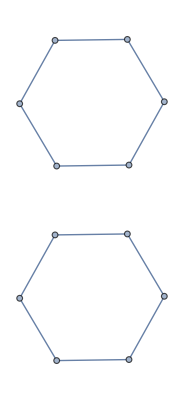

(n r (2+(-2+3 n) r+2 n^2 r^2+n^2 (2+n) r^3))/(3+4 n+n^2)

```mathematica
gg={
{{"Π",1,"out",1},{"U",1,"in",1}},
{{"U",1,"out",1},{"U",2,"out",1}},
{{"U",2,"in",1},{"Π",2,"in",1}},
{{"Π",2,"out",1},{"U*",1,"out",1}},
{{"U*",1,"in",1},{"U*",2,"in",1}},
{{"U*",2,"out",1},{"Π",1,"in",1}},

{{"Π",3,"out",1},{"U",3,"in",1}},
{{"U",3,"out",1},{"U",4,"out",1}},
{{"U",4,"in",1},{"Π",4,"in",1}},
{{"Π",4,"out",1},{"U*",3,"out",1}},
{{"U*",3,"in",1},{"U*",4,"in",1}},
{{"U*",4,"out",1},{"Π",3,"in",1}}
};
visualizeTN[gg]
gge=integrateHaarUnitary[gg,"U",{n},{n},n];
visualizeTN[gge];
computeDiagram@gge
```

## ω^(2)=(TrWTrW - (TrW)^2)/(4(r(1-r))^2)

```mathematica
Limit[(computeDiagram@gge-(computeDiagram@ge)^2)/(4(r(1-r))^2),n->∞]//FullSimplify
```

1/2